# Free fall on a fixed center and harmonic oscillator.

## Newton’s equation for the free fall (Unnecessary constants have been removed) :

```mathematica
DSolve[{x''[t]==-1/x[t]^2,x[0]==1,x'[0]==0},x[t],t]
```

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem these solutions will be ignored, so some of the solutions will be lost.

{}

## That equation is best integrated analytically by considering the energy first integral, (x'[t]^2/2-1/x=E (=-1 on account of the particular initial conditions choosen)). Here is the solution in implicit form t=time(x) :

```mathematica
time[x_]:=(√(x(1-x))+  ArcCos[√x])/(√2)
```

```mathematica
x[t_]:=InverseFunction[time][t]
```

```mathematica
D[x[t],{t,2}]==-1/x[t]^2//FullSimplify
```

True

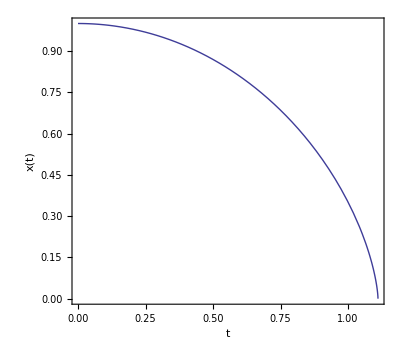

```mathematica
Plot[x[t],{t,0,π/(2 √2)},AspectRatio->Automatic,Axes->False,Frame->True,PlotStyle->Thick,FrameLabel->{"t","x(t)"},LabelStyle->Directive[Large,Bold]]
```

## A forward numerical integration suspects the presence of a singularity near t=1.11... :

```mathematica
NDSolve[{x''[t]==-1/x[t]^2,x[0]==1,x'[0]==0},x[t],{t,0,2}]
```

NDSolve::ndsz: At t == 1.11072, step size is effectively zero; singularity or stiff system suspected.

{{x[t]→InterpolatingFunction[{{0.,1.11072}},<>][t]}}

## Changing both dependant and independant variables in Mathematica :

1) The change of Sundman (x=X^2 and dt=X^2 dT) :

```mathematica
Dt[Dt[X[T]^2 ]/(X[T]^2 Dt[T])]/(X[T]^2 Dt[T])+1/X[T]^4//Simplify
```

(1-2 X'[T]^2+2 X[T] X''[T])/X[T]^4

```mathematica
1/2(Dt[X[T]^2 ]/(X[T]^2 Dt[T]))^2-1/X[T]^2==Energy//Simplify
```

(-1+2 X'[T]^2)/X[T]^2==Energy

Combining the two former equations leads to a harmonic oscillation of X as a function of T.

```mathematica
Plot[x[t],{t,0,π/(2 √2)},AspectRatio->Automatic,Axes->False,Frame->True,PlotStyle->Thick,FrameLabel->{"t","x(t)"},LabelStyle->Directive[Large,Bold]]
```

-Graphics-

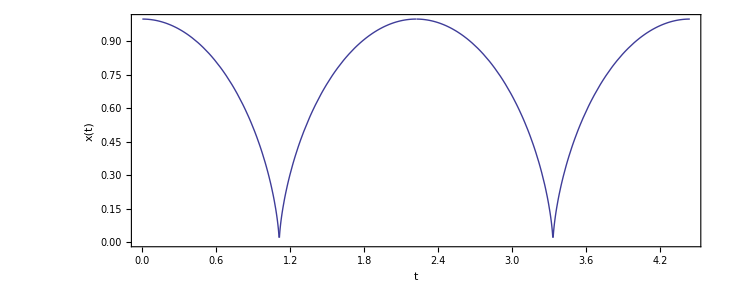

```mathematica
Plot[Piecewise[{{x[t],0<t<π/(2 √2)},{x[(2π)/(2 √2)-t],π/(2 √2)<t <(2π)/(2 √2)},{x[t-(2π)/(2 √2)],(2π)/(2 √2)<t<(3π)/(2 √2)},{x[(4π)/(2 √2)-t],(3π)/(2 √2)<t <(4π)/(2 √2)}}],{t,0,(4π)/(2 √2)},AspectRatio->Automatic,Axes->False,Frame->True,PlotStyle->Thick,FrameLabel->{"t","x(t)"},LabelStyle->Directive[Large,Bold]]
```

2) No monomial point transformation, x=X^aT^b and t=X^cT^d (where a, b, c, d are constants whatever their numerical values) can achieve such a  reduction :

```mathematica
Dt[Dt[X[T]^a T^b]/Dt[X[T]^c T^d]]/Dt[X[T]^c T^d]+1/(X[T]^(2a) T^(2b))/.{Dt[a]->0,Dt[b]->0,Dt[c]->0,Dt[d]->0}//Simplify
```

1/(d X[T]+c T X'[T])^3 T^(-2 (b+d)) X[T]^(-2 (a+c)) (b (b-d) d T^(3 b) X[T]^(3+3 a)+d^3 T^(2 d) X[T]^(3+2 c)+3 c d^2 T^(1+2 d) X[T]^(2+2 c) X'[T]-(b c (-1-2 a+c)+a (1-a+2 c) d) T^(2+3 b) X[T]^(1+3 a) X'[T]^2+3 c^2 d T^(2+2 d) X[T]^(1+2 c) X'[T]^2+a (a-c) c T^(3+3 b) X[T]^(3 a) X'[T]^3+c^3 T^(3+2 d) X[T]^(2 c) X'[T]^3+T^(1+3 b) X[T]^(2+3 a) ((b^2 c-a (-1+d) d-b (c-2 a d+2 c d)) X'[T]+(-b c+a d) T X''[T]))

```mathematica
Together[1/2(Dt[X[T]^a T^b]/Dt[X[T]^c T^d])^2-1/(X[T]^a T^b)/.{Dt[a]->0,Dt[b]->0,Dt[c]->0,Dt[d]->0}]//Simplify
```

1/(2 (d X[T]+c T X'[T])^2)T^(-b-2 d) X[T]^(-a-2 c) (b^2 T^(3 b) X[T]^(2+3 a)-2 d^2 T^(2 d) X[T]^(2+2 c)+2 a b T^(1+3 b) X[T]^(1+3 a) X'[T]-4 c d T^(1+2 d) X[T]^(1+2 c) X'[T]+a^2 T^(2+3 b) X[T]^(3 a) X'[T]^2-2 c^2 T^(2+2 d) X[T]^(2 c) X'[T]^2)